```mathematica
Pristine ZrC electron transport;
```

#### Some basic information;

```mathematica
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850};
tempps={0,10,300,500,760,1000,1500,1900,2500,3200,3800};
temppps=tempps[[2;;11]];
temps2={300,300,760,1900,2500,3200,3800};
temps3={300,760,1900,2500,3200,3800};
THz2meV=1/4.135665538536;K2meV=0.086173324;kjmol2evatom=1/(96.487*64);
Nat=64;Natvac=63;mass={91.224,12.0107,1};
ang2bohr=1/0.529177208;ev2har=1/27.211396;kB=1000*8.617332478*10^−5;
eVperAng2harperbohr=ev2har/ang2bohr;eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;
HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
(*Constant, Fermi-Dirac and Fermi-Dirac changing with energy*)
K2eV=8.617332478*10^−5;
fermiDirac[energy_,temp_]:=1/(Exp[energy/(K2eV*temp)]+1)
(*define sigma and8 kappa kernels*)
(*temp in energy units*)
sigmaK[energy_,temp_]:=-D[fermiDirac[energy,temp],energy]
kappaK[energy_,temp_]:=-(1/temp)*(energy^2)*D[fermiDirac[energy,temp],energy]
eV2ryd=1/13.605698066;ryd2eV=13.605698066;
```

#### Import data;

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/NEB/FINAL_PATHS_FOR_PAPER/"];
file={"3_vol_temp_dist_energy"};
NEBdata=Table[ReadList[file[[i]],{Number, Number,Number, Number,Number, Number,Number, Number,Number, Number,Number, Number,Number}],{i,1,1}][[1]];
```

```mathematica
Transpose[NEBdata]
```

{{0,1,2,3,4},{4.6583,4.6583,4.6583,4.6583,4.6583},{0,0,0,0,0},{0.,0.540279,0.881051,1.93139,4.34964},{0.,0.459286,0.390465,0.995135,-3.36282},{4.759,4.759,4.759,4.759,4.759},{2479,2479,2479,2479,2479},{0.,0.505926,0.917487,2.29007,3.5768},{0.,0.415663,0.297066,1.18229,-2.82737},{4.85,4.85,4.85,4.85,4.85},{3821,3821,3821,3821,3821},{0.,0.491838,0.973187,2.42791,3.66887},{0.,0.408561,0.224986,1.4023,-2.07754}}

```mathematica
index=Transpose[NEBdata][[{1}]][[1]]
vols=Transpose[NEBdata][[{2,6,10}]]
temp=Transpose[NEBdata][[{3,7,11}]]
dist=Transpose[NEBdata][[{4,8,12}]]
e0s=Transpose[NEBdata][[{5,9,13}]]
```

{0,1,2,3,4}

{{4.6583,4.6583,4.6583,4.6583,4.6583},{4.759,4.759,4.759,4.759,4.759},{4.85,4.85,4.85,4.85,4.85}}

{{0,0,0,0,0},{2479,2479,2479,2479,2479},{3821,3821,3821,3821,3821}}

{{0.,0.540279,0.881051,1.93139,4.34964},{0.,0.505926,0.917487,2.29007,3.5768},{0.,0.491838,0.973187,2.42791,3.66887}}

{{0.,0.459286,0.390465,0.995135,-3.36282},{0.,0.415663,0.297066,1.18229,-2.82737},{0.,0.408561,0.224986,1.4023,-2.07754}}

```mathematica
Flatten[{dist[[1]],2dist[[1]][[-1]]-dist[[1]][[-2]]}]
```

{0.,0.540279,0.881051,1.93139,4.34964,6.76788}

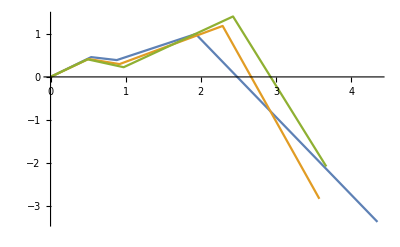

```mathematica
diste0s=Table[Transpose@{dist[[i]],e0s[[i]]},{i,1,3}];
ListLinePlot@diste0s
```

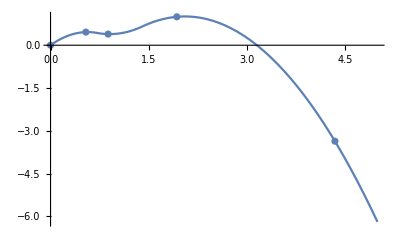

```mathematica
Show[{Plot[Interpolation[diste0s[[1]],Method->"Spline",InterpolationOrder->2][x],{x,0,5}],ListPlot@diste0s[[1]]}]
```

```mathematica
diste0sGP=Table[Flatten[{#1->#2}&@@@diste0s[[i]]],{i,1,3}]
pdiste0sGP=Table[Predict[diste0sGP[[i]],Method->"GaussianProcess"],{i,1,3}]
```

{{0.→0.,0.540279→0.459286,0.881051→0.390465,1.93139→0.995135,4.34964→-3.36282},{0.→0.,0.505926→0.415663,0.917487→0.297066,2.29007→1.18229,3.5768→-2.82737},{0.→0.,0.491838→0.408561,0.973187→0.224986,2.42791→1.4023,3.66887→-2.07754}}

{PredictorFunction[…],PredictorFunction[…],PredictorFunction[…]}

```mathematica
Normal@pdiste0sGP[[1]];
```

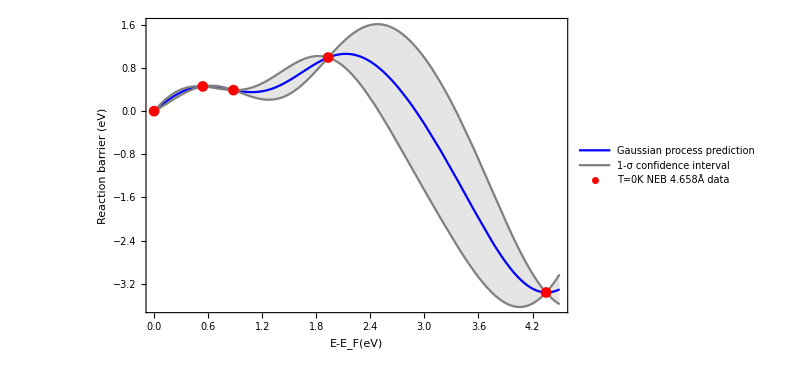

```mathematica
Show[Plot[{pdiste0sGP[[1]][x],pdiste0sGP[[1]][x]+StandardDeviation[pdiste0sGP[[1]][x,"Distribution"]],pdiste0sGP[[1]][x]-StandardDeviation[pdiste0sGP[[1]][x,"Distribution"]]},{x,0,4.5},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->x>1.1,PerformanceGoal->"Speed",PlotLegends->{"Gaussian process prediction","1-σ confidence interval"},Frame->True,FrameLabel->{"Reaction path (Å)","Reaction barrier (eV)"},ImageSize->600],ListPlot[List@@@diste0s[[1]],PlotStyle->Red,PlotLegends->{"T=0K NEB 4.658Å data"}]]
```

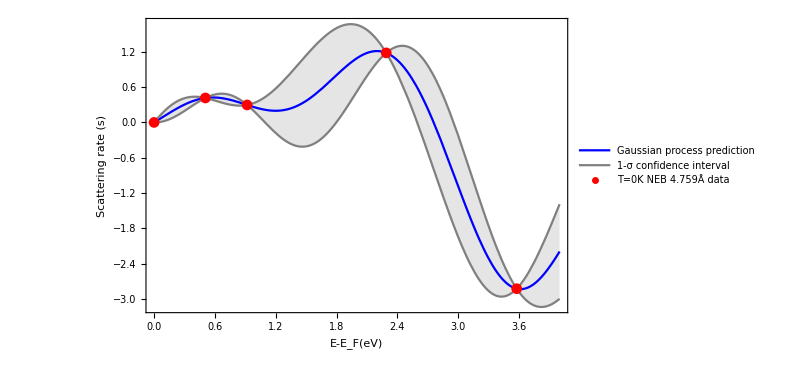

```mathematica
Show[Plot[{pdiste0sGP[[2]][x],pdiste0sGP[[2]][x]+StandardDeviation[pdiste0sGP[[2]][x,"Distribution"]],pdiste0sGP[[2]][x]-StandardDeviation[pdiste0sGP[[2]][x,"Distribution"]]},{x,0,4},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->x>1.1,PerformanceGoal->"Speed",PlotLegends->{"Gaussian process prediction","1-σ confidence interval"},Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (s)"},ImageSize->600],ListPlot[List@@@diste0s[[2]],PlotStyle->Red,PlotLegends->{"T=0K NEB 4.759Å data"}]]
```

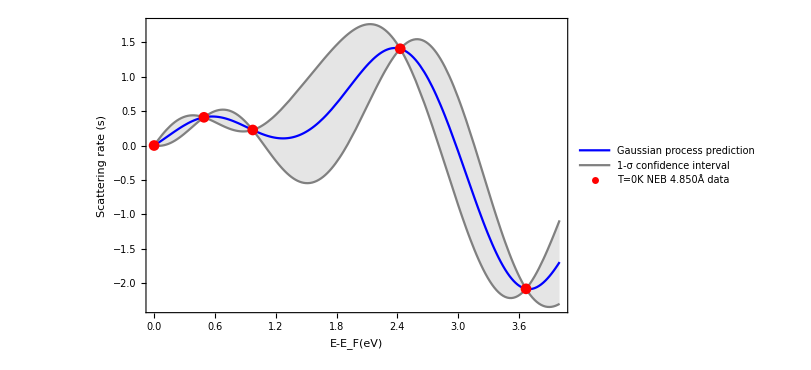

```mathematica
Show[Plot[{pdiste0sGP[[3]][x],pdiste0sGP[[3]][x]+StandardDeviation[pdiste0sGP[[3]][x,"Distribution"]],pdiste0sGP[[3]][x]-StandardDeviation[pdiste0sGP[[3]][x,"Distribution"]]},{x,0,4},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->x>1.1,PerformanceGoal->"Speed",PlotLegends->{"Gaussian process prediction","1-σ confidence interval"},Frame->True,FrameLabel->{"E-E_F(eV)","Scattering rate (s)"},ImageSize->600],ListPlot[List@@@diste0s[[3]],PlotStyle->Red,PlotLegends->{"T=0K NEB 4.850Å data"}]]
```

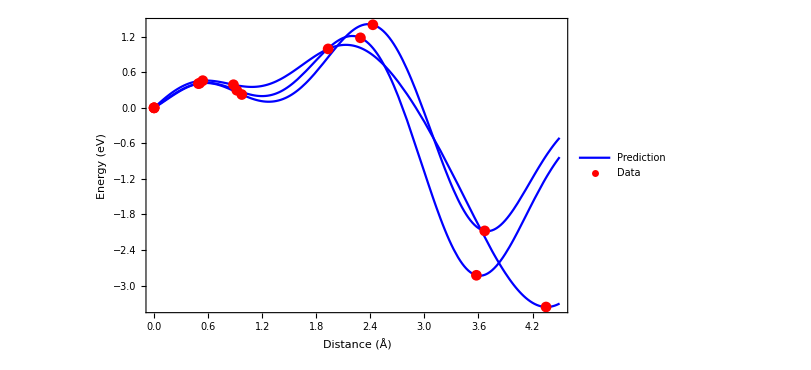

```mathematica
plota=Show[Plot[Evaluate@Table[{pdiste0sGP[[i]][x]},{i,1,3}],{x,0,4.5},PlotStyle->{Blue},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction"},Frame->True,FrameLabel->{"Distance (Å)","Energy (eV)"},ImageSize->600],ListPlot[Table[List@@@diste0s[[i]],{i,1,3}],PlotStyle->Red,PlotLegends->{"Data"}]]
```

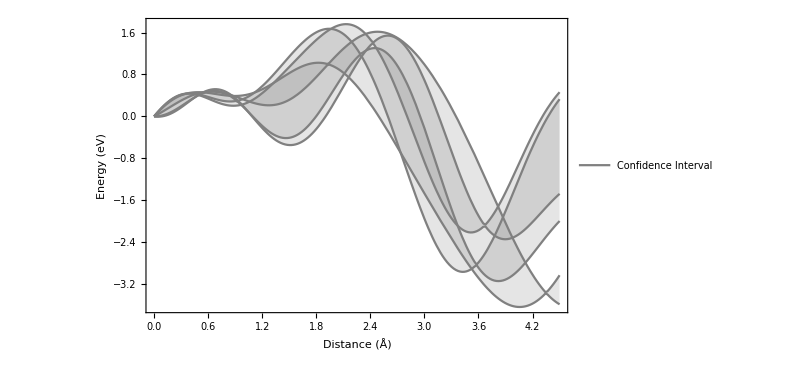

```mathematica
plotb=Show[Plot[Evaluate@Table[{pdiste0sGP[[i]][x]+StandardDeviation[pdiste0sGP[[i]][x,"Distribution"]],pdiste0sGP[[i]][x]-StandardDeviation[pdiste0sGP[[i]][x,"Distribution"]]},{i,1,3}],{x,0,4.5},PlotStyle->{Gray,Gray},Filling->{1->{2},3->{4},5->{6}},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Confidence Interval"},Frame->True,FrameLabel->{"Distance (Å)","Energy (eV)"},ImageSize->600]]
```

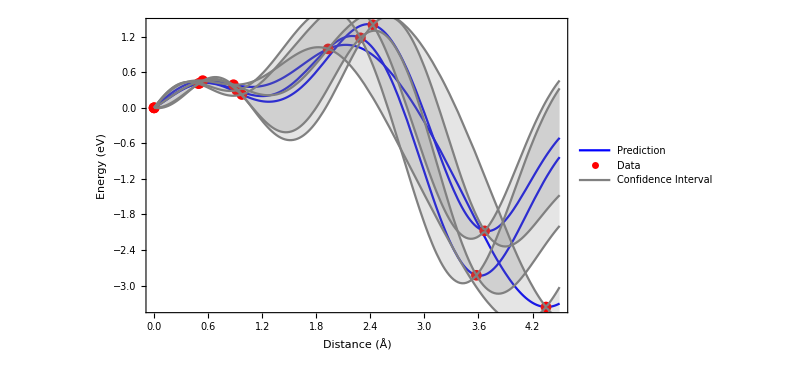

```mathematica
Show[{plota,plotb}]
```

```mathematica
volshort=Table[vols[[i]][[1]],{i,1,3}]
```

{4.6583,4.759,4.85}

```mathematica
list2=Partition[Flatten@Table[Join@Table[{volshort[[j]],i/4,pdiste0sGP[[j]][i/10]},{i,1,50}],{j,1,3}],3];
```

```mathematica
diste0sGP=Table[Flatten[{#1->#2}&@@@diste0s[[i]]],{i,1,3}]
pdiste0sGP=Table[Predict[diste0sGP[[i]],Method->"GaussianProcess"],{i,1,3}]
```

```mathematica
diste0s[[1]]
```

```mathematica
Flatten[{#1->#2}&@@@diste0s[[1]]]
```

{0.→0.,0.540279→0.459286,0.881051→0.390465,1.93139→0.995135,4.34964→-3.36282}

```mathematica
volDistE0GP={#1->#2&&#3}&@@@list2;
```

```mathematica
Predict[volDistE0GP[[1]],Method->"GaussianProcess"]
```

Predict::mlincfttp: Incompatible variable type (Numerical) and variable value (1/4&&0.137491).

Predict[{4.6583→1/4&&0.137491},Method→GaussianProcess]

```mathematica
ListPlot3D[list2]
```

-Graphics3D-

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/FRENKEL_RESULTS/Tall/Frenkel_Tall"];
fileFFE={"e0.out.m","e0_FS.out.m","VFE.Fqh_FS.out.m","VFE.Fqh_Fel_FS.out.m","VFE.Fqh_Fel.out.m","VFE.Fqh.out.m"};
FFEdata=Table[ReadList[fileFFE[[i]],{Number, Number}],{i,1,4}];
```

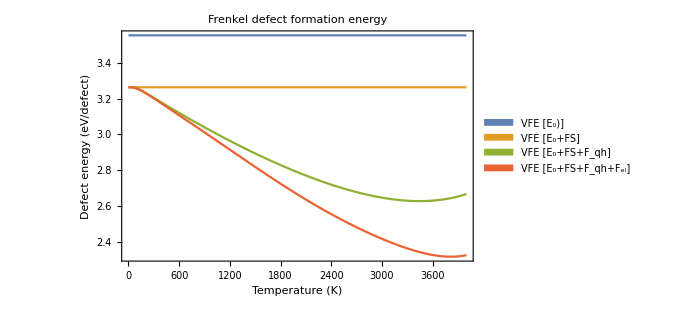

```mathematica
ListLinePlot[FFEdata,PlotLabel->"Frenkel defect formation energy",FrameLabel->{"Temperature (K)","Defect energy (eV/defect)"},Frame->True,ImageSize->500,PlotLegends->Placed[SwatchLegend[{"VFE [E_0)]","VFE [E_0+FS]","VFE [E_0+FS+F_qh]","VFE [E_0+FS+F_qh+F_el]"}],{0.84,0.5}]]
```

```mathematica
gibbs=Transpose[VFEdata[[4]]][[2]];
ttemp=Transpose[VFEdata[[4]]][[1]];
```

```mathematica
K2eV
```

0.0000861733

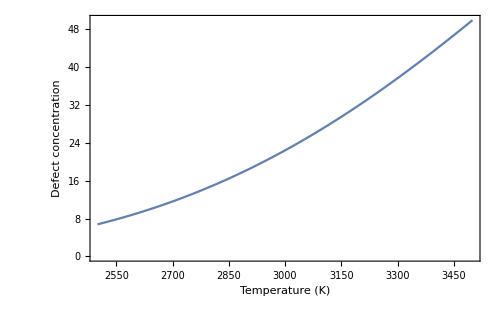

```mathematica
multiplicity=24;
tgibbsTrimer=Transpose@{ttemp,100*multiplicity*Exp[-gibbs/(2K2eV*ttemp)]};
ListLinePlot[tgibbsTrimer[[2500;;3500]],FrameLabel->{"Temperature (K)","Defect concentration"},Frame->True,ImageSize->500]
```

```mathematica
gibbs[[-1]]
gibbs[[-1]]-deltaDimer
```

2.32479

2.71279

```mathematica
gibbs[[1]]
```

3.26336

```mathematica
(*Trimer is lowest energy defect at 3.622, trimer is next 4.010 then 4.628 *)
deltaDimer=3.622-4.010
deltaTrimerUnbound=3.622-4.628
(*Bound dimer*)
tgibbsDimer=Transpose@{ttemp,100*multiplicity*Exp[-(gibbs-deltaDimer)/(2K2eV*ttemp)]};
(*Unbound trimer*)
tgibbsTrimerUnbound=Transpose@{ttemp,100*multiplicity*Exp[-(gibbs-deltaTrimerUnbound)/(2K2eV*ttemp)]};
(*Total*)
total=Transpose[{Transpose[tgibbsDimer[[2000;;3800]]][[1]],Transpose[tgibbsTrimer[[2000;;3800]]][[2]]+Transpose[tgibbsDimer[[2000;;3800]]][[2]]}];
```

-0.388

-1.006

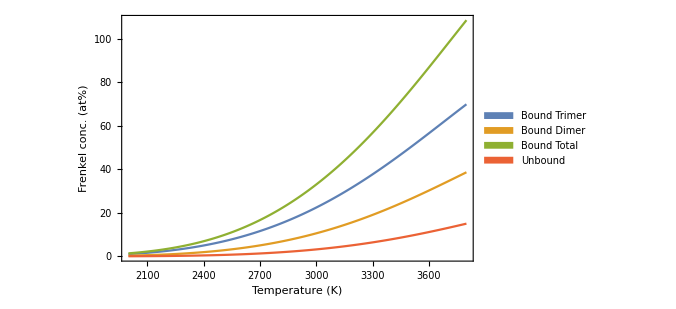

```mathematica
ListLinePlot[{tgibbsTrimer[[2000;;3800]],tgibbsDimer[[2000;;3800]],total,tgibbsTrimerUnbound[[2000;;3800]]},FrameLabel->{"Temperature (K)","Frenkel conc. (at%)"},Frame->True,ImageSize->500,PlotLegends->Placed[SwatchLegend[{"Bound Trimer","Bound Dimer","Bound Total","Unbound"}],{0.15,0.5}],PlotRange->All]
```

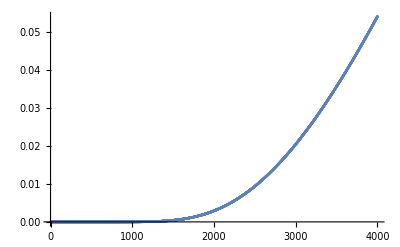

```mathematica
a=Exp[-3.622/(K2eV*ttemp)];
b=Exp[-4.628/(K2eV*ttemp)];
ListPlot[b[[1;;4000]]/a[[1;;4000]]]
```

```mathematica
1/(b[[2000]]/a[[2000]])
```

342.775